```mathematica
(*Cykliczność:*)
```

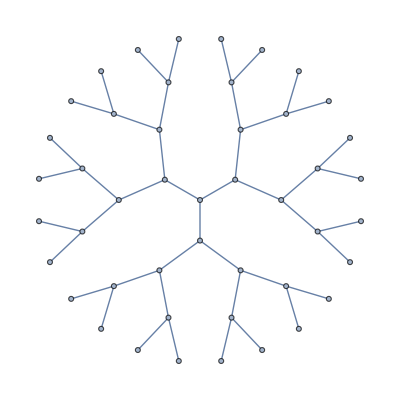

```mathematica
g = GraphData[{"CayleyTree",{3,4}}]
```

```mathematica
AcyclicGraphQ[g]
```

True

```mathematica
Export["/home/kacper/current/temp_asid2/g1",AdjacencyMatrix[g] , "Table"]
```

/home/kacper/current/temp_asid2/g1

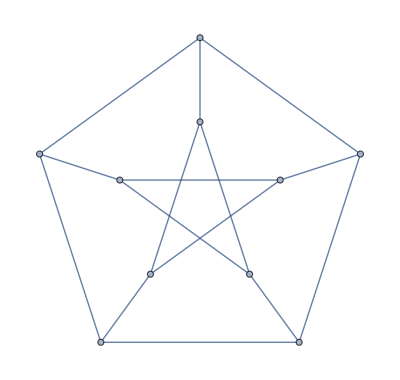

```mathematica
g = PetersenGraph[5,2]
```

```mathematica
AcyclicGraphQ[g]
```

False

```mathematica
Export["/home/kacper/current/temp_asid2/g2",AdjacencyMatrix[g] , "Table"]
```

/home/kacper/current/temp_asid2/g2

```mathematica
g = -Graphics-;
```

```mathematica
AcyclicGraphQ[g]
```

False

```mathematica
Export["/home/kacper/current/temp_asid2/g3",AdjacencyMatrix[g] , "Table"]
```

/home/kacper/current/temp_asid2/g3

```mathematica
(*Spójność:*)
```

```mathematica
g = GraphData[{"CayleyTree",{3,4}}]
```

-Graphics-

```mathematica
VertexList[g]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46}

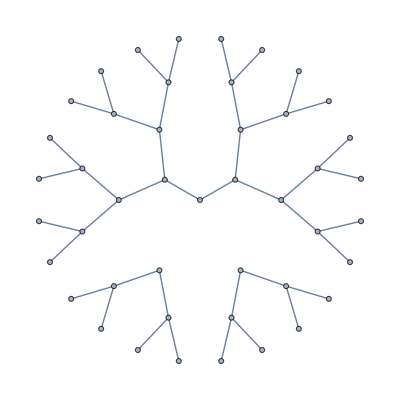

```mathematica
g = VertexDelete[g,3]
```

```mathematica
ConnectedGraphQ[g]
```

False

```mathematica
Export["/home/kacper/current/temp_asid2/h1",AdjacencyMatrix[g] , "Table"]
```

/home/kacper/current/temp_asid2/h1

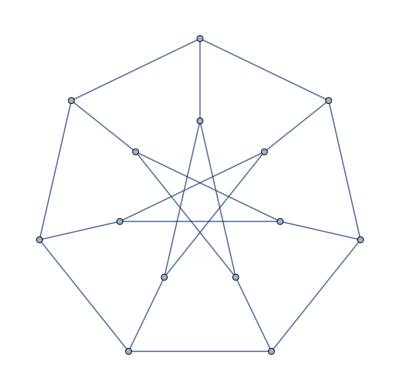

```mathematica
g = PetersenGraph[7,3]
```

```mathematica
VertexList[g]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14}

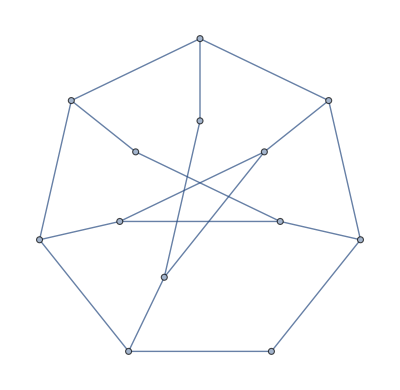

```mathematica
g = VertexDelete[g , 3]
```

```mathematica
ConnectedGraphQ[g]
```

True

```mathematica
Export["/home/kacper/current/temp_asid2/h2",AdjacencyMatrix[g] , "Table"]
```

/home/kacper/current/temp_asid2/h2

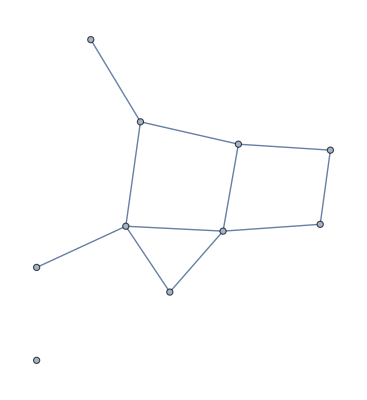

```mathematica
g = RandomGraph[{10,11}]
```

```mathematica
VertexList[g]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ConnectedGraphQ[g]
```

False

```mathematica
Export["/home/kacper/current/temp_asid2/h3",AdjacencyMatrix[g] , "Table"]
```

/home/kacper/current/temp_asid2/h3